```mathematica
SetDirectory[NotebookDirectory[]];
robot0Data = Import["fish_robot_state_data0.csv","Table"];
robot1Data = Import["fish_robot_state_data1.csv","Table"];
targetData = Import["fish_target_state_data.csv","Table"];
timeStep = 0.05;
robot0Interp = Interpolation[Table[{timeStep *i, robot0Data[[i+1]]},{i,0,Length@robot0Data-1}]];
robot1Interp = Interpolation[Table[{timeStep *i, robot1Data[[i+1]]},{i,0,Length@robot1Data-1}]];
targetInterp = Interpolation[Table[{timeStep *i, targetData[[i+1]]},{i,0,Length@targetData-1}]];
delay = 0.5;
robot1Track[tt_]:=ParametricPlot[robot1Interp[t][[1;;2]], {t,tt-delay,tt},PlotRange->{{0,1},{0,1}}]
robot0Track[tt_]:=ParametricPlot[robot0Interp[t][[1;;2]], {t,tt-delay,tt},PlotRange->{{0,1},{0,1}},PlotStyle->Magenta]
targetTrack[tt_]:=Graphics[{Red,Circle[targetInterp[tt][[1;;2]],0.05]}](*ParametricPlot[spotlightInterp[t][[1;;2]], {t,0,tt},PlotRange->{{0,1},{0,1}}, PlotStyle->Red]*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
robot0Data = Import["robot_state_data0.csv","Table"];
robot1Data = Import["robot_state_data1.csv","Table"];
targetData = Import["target_state_data.csv","Table"];
timeStep = 0.05;
robot0Interp = Interpolation[Table[{timeStep *i, robot0Data[[i+1]]},{i,0,Length@robot0Data-1}]];
robot1Interp = Interpolation[Table[{timeStep *i, robot1Data[[i+1]]},{i,0,Length@robot1Data-1}]];
targetInterp = Interpolation[Table[{timeStep *i, targetData[[i+1]]},{i,0,Length@targetData-1}]];
delay = 0.5;
robot1Track[tt_]:=ParametricPlot[robot1Interp[t][[1;;2]], {t,tt-delay,tt},PlotRange->{{0,1},{0,1}}]
robot0Track[tt_]:=ParametricPlot[robot0Interp[t][[1;;2]], {t,0,tt+0.01},PlotRange->{{0,1},{0,1}},PlotStyle->Magenta]
targetTrack[tt_]:=Graphics[{Red,Circle[targetInterp[tt][[1;;2]],0.05]}](*ParametricPlot[spotlightInterp[t][[1;;2]], {t,0,tt},PlotRange->{{0,1},{0,1}}, PlotStyle->Red]*)
```

```mathematica
covarData = Import["target_covar_data0.csv","Table"];
covarInterp = Interpolation[Table[{timeStep*i,covarData[[i+1]]},{i,0,Length@covarData-1}]];
targetMeanData = Import["target_mean_data0.csv","Table"];
targetMeanInterp = 
Interpolation[
Table[
{timeStep*i, targetData[[i+1]]},
{i,0,Length@targetMeanData-1}
]
];
gaussDist[t_] := PDF[MultinormalDistribution[targetInterp[t], ArrayReshape[covarInterp[t],{2,2}]],{x,y}];

listPlots = Table[
Graphics[Show[{
DensityPlot[gaussDist[t],{x,0,1},{y,0,1},PlotRange->All, ColorFunction->"SunsetColors"],
targetTrack[t],
robot0Track[t],robot1Track[t]
}]],
{t,0,20,0.1}];
```

InterpolatingFunction::dmval: Input value {-0.49999} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.39999} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.29999} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
ListAnimate[listPlots]
```

```mathematica
Animate[Graphics[Show[{robot0Track[t],robot1Track[t],targetTrack[t]}]],{t,delay,40,0.1}]
```

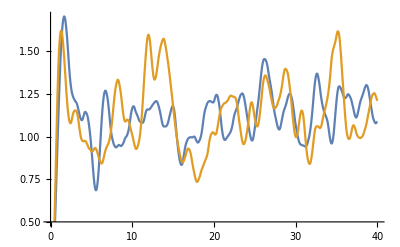

```mathematica
Plot[{robot1Interp[t][[3]],robot0Interp[t][[3]]},{t,0,40}]
```

```mathematica
dplot[t_] :=Show[DensityPlot[gaussDist[t],{x,0,1},{y,0,1},PlotRange->All, ColorFunction->ColorData[{"GrayTones","Reverse"}],
Frame-> False
],
robot0Track[t]];
level=0;
graph3d[t_]:=Graphics3D[{Texture[dplot[t]],EdgeForm[],Polygon[{{0,0,level},{1,0,level},{1,1,level},{0,1,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
robot3DPlot[t_] := ParametricPlot3D[robot0Interp[tt][[1;;3]],{tt,0,t+0.01},PlotRange->{{0,1},{0,1},{0,1.5}},
Axes-> False];
allPlots[t_]:=Show[graph3d[t],Graphics3D@quadGraph[robot0Interp[t][[1;;3]],robot0Interp[t][[4;;6]]],BoxRatios-> {1,1,0.5}]
testPlots = Table[allPlots[t],{t,0,20-0.1,0.1}];
```

```mathematica
quadGraph[xpos_,ang_] := DibujaQuadrotor[xpos,ang,"zyx"];
```

```mathematica
ListAnimate[testPlots]
```

## Quadcopter model

```mathematica
DibujaQuadrotor[pos_,ang_,convencion_]:=
Module[{helic,aro,rotor},
(* Chasis *)
brazos={RGBColor[1,0,1],Cylinder[{{-0.5,0,0},{0.5,0,0}},0.025],
              Cylinder[{{0,-0.5,0},{0,0.5,0}},0.025],
              ColorData["Atoms"]["Cl"]};
(* Cuerpo *)
cuerp={RGBColor[0,1,0],Scale[Sphere[],{0.19,0.12,0.1},{0,0,0}]};
cuerpo = Rotate[cuerp,Pi/4,{0,0,1}];
(* Motores *)
rotor[posx_,posy_,posz_]={ColorData["Atoms"]["S"],Cylinder[{{posx,posy,posz},{posx,posy,1.5}},0.25],
Cylinder[{{posx,posy,posz},{posx,posy,1}},0.5]};
motores={rotor[-5,0,0],rotor[0,-5,0],rotor[5,0,0],rotor[0,5,0]};
(* Helices con aros esternos *)
helic[x_,y_,z_] = {Opacity[0.3],ColorData["HTML"]["Blue"],(*EdgeForm[Opacity[.1]]*),Cylinder[{{{x,y,z-0.01},{x,y,z}}},0.3]};
aro[x_,y_,z_]={ColorData["HTML"]["Gray"],Thick,Opacity[.01],Line[Table[{0.03Sin[t]+x,0.03Cos[t]+y,z},{t,0,0.2Pi+0.5,0.1}]]};
aros={aro[-0.5,0,0.15],aro[0,-0.5,0],aro[0.5,0,0.15],aro[0,0.5,0.15]};
helices={helic[-0.5,0,0], helic[0.5,0,0], helic[0,-0.5,0], helic[0,0.5,0]};
completo=Rotate[{Opacity[0.9],brazos,cuerpo,helices},Pi/4,{0,0,1}];
(* Vectores de Rotación *)
ex={1,0,0};ey={0,1,0};ez={0,0,1};
If[convencion=="xyz",
Gϕ=ex;Gθ=ey;Gψ=ez;];
If[convencion=="xzx",
Gϕ=ex;Gθ=ez;Gψ=ex;];
If[convencion=="xzy",
Gϕ=ex;Gθ=ez;Gψ=ey;];
If[convencion=="yxy",
Gϕ=ey;Gθ=ex;Gψ=ey;];
If[convencion=="xyx",
Gϕ=ex;Gθ=ey;Gψ=ex;];
If[convencion=="yxz",
Gϕ=ey;Gθ=ex;Gψ=ez;];
If[convencion=="yzx",
Gϕ=ey;Gθ=ez;Gψ=ex;];
If[convencion=="yzy",
Gϕ=ey;Gθ=ez;Gψ=ey;];
If[convencion=="zxy",
Gϕ=ez;Gθ=ex;Gψ=ey;];
If[convencion=="zxz",
Gϕ=ez;Gθ=ex;Gψ=ez;];
If[convencion=="zyx",
Gϕ=ez;Gθ=ey;Gψ=ex;];
If[convencion=="zyz",
Gϕ=ez;Gθ=ey;Gψ=ez;];
(* Rotación del Quadrotor y esfera *)
Gfϕ=Rotate[completo,ang[[3]],Gϕ];
Gfθ=Rotate[Gfϕ,ang[[2]],Gθ];
Gfψ=Rotate[Gfθ,ang[[1]],Gψ];
(*Gfψ = GeometricTransformation[completo, RR];*)
Gf = Scale[Translate[Gfψ,pos],0.1];
(* Gráfica *)
(*Show[
Graphics3D[Gf,
Axes-> None, AxesOrigin-> {0,0,0},Boxed->False,Lighting->{{"Ambient",GrayLevel[.1]},{"Point",Gray,{1,1,10}},{"Point",Gray,{0,0,10}}},
                        PlotRange->25{{1,-1},{-1,1},{-1,1}},ViewVector->{2,2,2},ImageSize->{450,450}, SphericalRegion-> True
]
]*)
Return[Gf];
]
```